```mathematica
(* Helper Functions *)
t1d[params_] := Transpose[{params}] 
listProduct[l_] := Product[l[[i]],{i,1,Length[l]}]
grabElements[l_,e_] := Map[l[[#]]&,e] 
generateFluxCoefficients[GE_,S_] :=Map[listProduct[grabElements[GE,Position[#,_?Positive][[All,1]]]]&,Transpose[S]]
solveForParameters[v_,coeff_]  := MapThread[#1/#2&,{v,coeff}]
solveForFluxes[SS_,fluxes_,S_,x1_,x2_,x3_,error_] := fluxes /.NMinimize[{Norm[SS - S.t1d[fluxes]],fluxes ≥ 0.001,fluxes[[-3]] ==x1,fluxes[[-2]] ==x2,fluxes[[-1]]==x3},fluxes,AccuracyGoal->4][[2]];
FVA[SS_,fluxes_,S_] := {
Map[NMinimize[
{#,fluxes>=.001 ,fluxes <= 1000,Norm[SS-S.t1d[fluxes]] == 0},fluxes,MaxIterations -> 1000,AccuracyGoal->2]&,fluxes][[All,1]],
Map[NMaximize[
{#,fluxes>=.001 ,fluxes <= 1000,Norm[SS-S.t1d[fluxes]] == 0},fluxes,MaxIterations -> 1000,AccuracyGoal->2]&,fluxes][[All,1]]};
getTermFromReaction[SCol_,species_,rateConstant_,fluxes_] := 
Module[{term=rateConstant},
Map[(term = term *(species[[#]])^Abs[SCol[[#]]])&,Position[SCol,_?Negative][[All,1]]];
If[term == rateConstant,term += rateConstant*fluxes[[Position[SCol,_?Positive][[1,1]]]]];
{Map[{SCol[[#]],species[[#]]}&,Range[Length[SCol]]],
term}
]
addTermToReaction[reactionList_,species_,term_,toReactions_] := 
Module[{temp},
temp = reactionList;
Map[
temp[[Position[species,#[[2]]][[1,1]]]] += #[[1]]*term &,
toReactions];
temp]
generateExpressions[S_,species_,IC_,var_,rateConstants_,fluxes_] := 
Module[{reactionList = ConstantArray[0,Length[species]],allReactions},
allReactions = MapThread[getTermFromReaction[#1,species,#2,fluxes]&,{Transpose[S],rateConstants}];
allReactions = Total[Map[addTermToReaction[reactionList,species,#[[2]],#[[1]]]&,allReactions]];
Join[
MapThread[#2 == #1&,{allReactions /. Map[# -> #[var]&,species],species /. Map[# -> #'[var]&,species]}],
MapThread[#2 == #1&,{IC,species /. Map[# -> #[0]&,species]}]
]
]
```

For the given toy reaction network:
b ->a 
a ->b
b -> c + d
d + e -> f
f -> d + e
e + a -> g
a + d -> e
aE->a
->aE (input glucose)
c->cE (measured)
g->gE (measured)

```mathematica
(*Reaction Network*)
S = {{1,-1,0,0,0,-1,-1,1,0,0,0},{-1,1,-1,0,0,0,0,0,0,0,0},{0,0,1,0,0,0,0,0,0,-1,0},{0,0,1,-1,1,0,-1,0,0,0,0},{0,0,0,-1,1,-1,1,0,0,0,0},{0,0,0,1,-1,0,0,0,0,0,0},{0,0,0,0,0,1,0,0,0,0,-1},{0,0,0,0,0,0,0,-1,1,0,0},{0,0,0,0,0,0,0,0,0,1,0},{0,0,0,0,0,0,0,0,0,0,1}};
Clear[v1,v2,v3,v4,v5,v6,v7,v8,v9,v10,v11,a,b,c,d,e,f,g,aE,cE,gE]
MatrixRank[S]
Length[S]
fluxes = {v1,v2,v3,v4,v5,v6,v7,v8,v9,v10,v11};
species = {a,b,c,d,e,f,g,aE,cE,gE};
SS  = ConstantArray[0,{Length[S],1}];
error = .001;
tmax =1000;
bolus = 10;

Print[SS//MatrixForm,"=",S//MatrixForm,t1d[fluxes] //MatrixForm]
```

9

10

(0
0
0
0
0
0
0
0
0
0)=(1 | -1 | 0 | 0 | 0 | -1 | -1 | 1 | 0 | 0 | 0
-1 | 1 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 1 | -1 | 1 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 1 | -1 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1)(v1
v2
v3
v4
v5
v6
v7
v8
v9
v10
v11)

```mathematica
(*Find the maximum flux for each reaction individually *)
{fluxMinimum,fluxMaximum} =FVA[SS,fluxes,S]
Print[fluxMinimum // MatrixForm,"≤",t1d[fluxes] // MatrixForm, "≤" ,fluxMaximum // MatrixForm]
```

$Aborted

(0.00105123
0.0198502
0.001
0.00129773
0.00119629
0.001
0.0010001
0.001
0.001
0.00100025)≤(v1
v2
v3
v4
v5
v6
v7
v8
v9
v10
v11)≤(0.00101208
152.955
0.001
178.869
148.552
0.001
0.001
0.00100222
0.00100004
0.00100042)

```mathematica
(*Measured flux values for WT*)
x1 = 1;
x2 = 1;
x3 = 1;
 fluxValuesWT = solveForFluxes[SS,fluxes,S,x1,x2,x3,error];
Print[t1d[fluxes] // MatrixForm,"=",t1d[fluxValuesWT] //MatrixForm] 
GEWT = RandomReal[{0,1},Length[S]];
fluxCoefficientsWT = solveForParameters[fluxValuesWT,generateFluxCoefficients[GEWT,S]];
baseLineKs = RandomReal[{0,10},Length[fluxValuesWT]];
(*AppendTo[baseLineKs,1];*)
expressions = generateExpressions[S,species,ConstantArray[0,Length[species]],t,baseLineKs,fluxValuesWT]
sol =NDSolve[expressions,species,{t,0,tmax}];
(*Map[Plot[Evaluate[#[t] /. sol],{t,0,1000},PlotRange -> All]&,species]*)
SSConcentrationsWT = Map[(Evaluate[#[tmax] /. sol])[[1]]&,species]
SSConcentrationsWT[[-3]]+=bolus
sol =NDSolve[generateExpressions[S[[All,Range[Length[S[[1,All]]]-1]]],species,SSConcentrationsWT,t,baseLineKs[[1;;-2]]],species,{t,0,tmax/10}];
Map[Plot[Evaluate[#[t] /. sol],{t,0,tmax/10},PlotRange -> All]&,{cE,gE}]
```

(v1
v2
v3
v4
v5
v6
v7
v8
v9
v10)=(0.885422
1.17114
0.571429
0.235445
0.235445
0.571429
0.42857
1.
1.
1.)

{Transpose^({1})[{t}]==0.+0.2208 aE[t]+9.98234 b[t]-6.33533 Transpose[{t}]-5.3032 d[t] Transpose[{t}]-4.63912 e[t] Transpose[{t}],b'[t]==0.-13.9813 b[t]+6.33533 Transpose[{t}],c'[t]==0.+3.99895 b[t]-2.67462 c[t],d'[t]==0.+3.99895 b[t]-4.21197 d[t] e[t]+3.0029 f[t]-5.3032 d[t] Transpose[{t}],e'[t]==0.-4.21197 d[t] e[t]+3.0029 f[t]+5.3032 d[t] Transpose[{t}]-4.63912 e[t] Transpose[{t}],f'[t]==0.+4.21197 d[t] e[t]-3.0029 f[t],g'[t]==0.-3.15676 g[t]+4.63912 e[t] Transpose[{t}],aE'[t]==0.-0.2208 aE[t],cE'[t]==0.+2.67462 c[t],gE'[t]==0.+3.15676 g[t],Transpose[{0}]==0,b[0]==0,c[0]==0,d[0]==0,e[0]==0,f[0]==0,g[0]==0,aE[0]==0,cE[0]==0,gE[0]==0}

{Transpose[{1000}],b[1000],c[1000],d[1000],e[1000],f[1000],g[1000],aE[1000],cE[1000],gE[1000]}

10+aE[1000]

{-Graphics-,-Graphics-}

{K}_m/{K}_wt = (3.52947
0.797529
1.16602
3.86934
2.74628
0.199259
1.17301
0.8
0.6
0.947997)

{52.1901,7.94983,1.07453,0.0144247,13.9467,0.046796,1.87353}

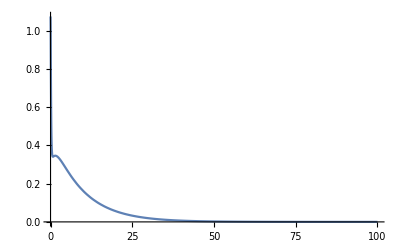
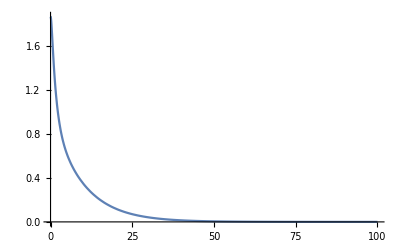

{K}_m/{K}_wt = (0.347976
2.96565
0.058579
0.79541
0.813894
0.0422596
1.21855)

```mathematica
x1 = .8;
x2 = .6;
x3 = 1;
 fluxValuesM = solveForFluxes[SS,fluxes,S,x1,x2,x3,error];
(*Print[a[fluxes] // MatrixForm,"=",a[fluxValuesM] //MatrixForm] *)
GEM = RandomReal[{0,1},Length[S]];
fluxCoefficientsM = solveForParameters[fluxValuesM,generateFluxCoefficients[GEM,S]];
ratioKs = fluxCoefficientsM/fluxCoefficientsWT;
Print["{K}_m/{K}_wt = ", ratioKs// MatrixForm]
expressions = generateExpressions[S,species,ConstantArray[0,Length[species]],t,baseLineKs*ratioKs,fluxValuesM];
sol =NDSolve[expressions,species,{t,0,tmax}];
(*Map[Plot[Evaluate[#[t] /. sol],{t,0,1000},PlotRange -> All]&,species]*)
SSConcentrationsM = Map[(Evaluate[#[tmax] /. sol])[[1]]&,species]
sol =NDSolve[generateExpressions[S[[All,Range[Length[S[[1,All]]]-1]]],species,Join[{bolus},SSConcentrationsM[[2;;-1]]],t,ratioKs[[1;;-2]]*baseLineKs[[1;;-2]]],species,{t,0,tmax/10}];
Map[Plot[Evaluate[#[t] /. sol],{t,0,tmax/10},PlotRange -> All]&,{s3,s7}]
```